```mathematica
vmtc={8760,8836,8960,9099,9214,9391,9517,9602,9735,9806,9922,9955,10117,10108,10095,10049,9796,9648,9717,9582,9564,9556,9603,9862,10065};
```

```mathematica
gp={1.09,1.07,1.08,1.11,1.2,1.2,1.03,1.14,1.48,1.42,1.35,1.56,1.85,2.27,2.57,2.8,3.25,2.35,2.78,3.52,3.62,3.51,3.36,2.43,2.14};
```

```mathematica
Graphics[{EdgeForm[Thick],White,Disk[{0,0},.1]}]
```

-Graphics-

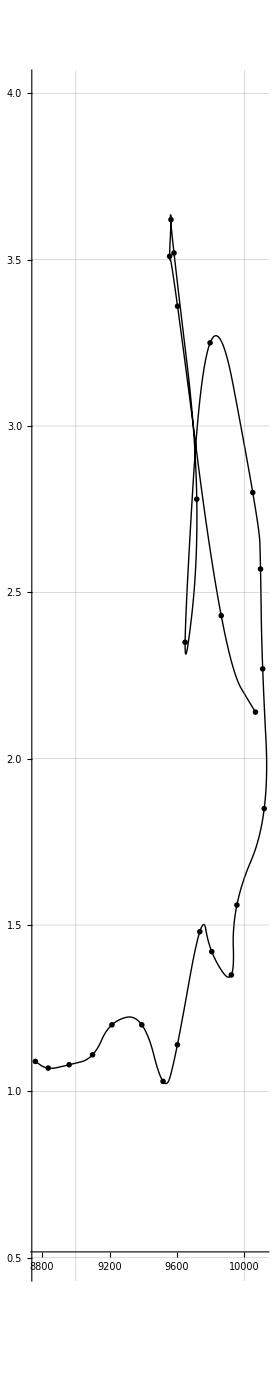

```mathematica
ListPlot[Transpose@{vmtc,gp},AspectRatio->5,Joined->True,InterpolationOrder->2,GridLines->{{9000,10000},{.5,1,1.5,2,2.5,3,3.5,4}},PlotRange->{.5,4},PlotStyle->{Thick,Black},PlotMarkers->Graphics[{EdgeForm[Thick],White,Disk[{0,0},Scaled[.02]]}],Mesh->Full]
```